# Complex Variables - HW 7 - question 4

### Define a function that allows us to plot the image plane for a set of set of points. I used a set of set to make plotting the graphic objects non connected independent objects.

```mathematica
makeImage[pts_,expr_,pltRange1_,PltRange2_]:=Module[{},
{
Graphics[{White, Thick, Line[#&/@pts]}, PlotRange -> {{-pltRange1,pltRange1},{-pltRange1,pltRange1}}, Axes -> True, Background -> GrayLevel[.6], ImageSize -> {300,300}, AxesLabel -> {Style["x",Italic], Style["y",Italic]},ImagePadding->20],

Graphics[{White, Thick, Line[{Re[expr /. z -> #[[1]] + ⅈ #[[2]]], Im[expr /. z -> #[[1]] + ⅈ #[[2]]]}& /@ #&/@pts]}, PlotRange -> {{-PltRange2,PltRange2},{-PltRange2,PltRange2}}, Axes -> True, Background -> RGBColor[.7, .5, .5], ImageSize -> {300,300}, AxesLabel -> {Style["u",Italic], Style["v",Italic]},ImagePadding->20]
}
]
```

### First we will plot expanding circles from .25 to 1.75 as these circles will either touch or go between the roots.

```mathematica
expr=(z+1)(z-.5)(z-1.5I)
```

(-0.5+z) ((0.-1.5 ⅈ)+z) (1+z)

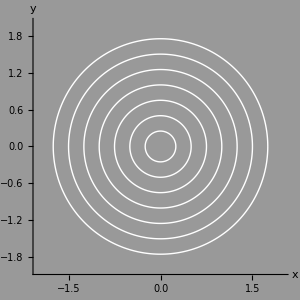
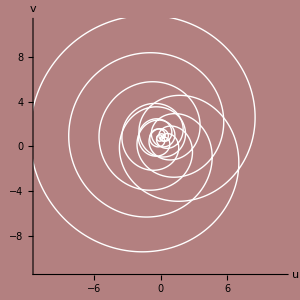

```mathematica
ang=Range[0Pi,2Pi,.001];
lists=Table[{r Cos[ang],r Sin[ang]},{r,Range[.25,1.75,.25]}];
pts=Transpose[#]&/@lists;
n=2;
m=11;
makeImage[pts,expr,n,m]
```

### Plot the same range but zoom in on the image

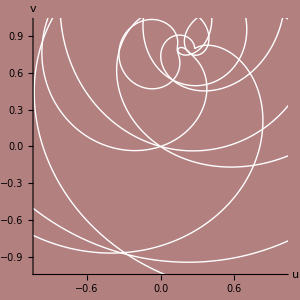
{-Graphics-,-Graphics-}

```mathematica
n=2;
m=1;
makeImage[pts,expr,n,m]
```

### Next we will plot expanding circles from with radius’s very close to the norm of the root of derivative of f. This is only done for one of the critical points to save ink!

```mathematica
makeImage2[pts_,expr_,pltRange1_]:=Module[{},
{
Graphics[{White, Thick, Line[#&/@pts]}, PlotRange -> {{-pltRange1,pltRange1},{-pltRange1,pltRange1}}, Axes -> True, Background -> GrayLevel[.6], ImageSize -> {300,300}, AxesLabel -> {Style["x",Italic], Style["y",Italic]},ImagePadding->20],

Graphics[{White, Thick, Line[{Re[expr /. z -> #[[1]] + ⅈ #[[2]]], Im[expr /. z -> #[[1]] + ⅈ #[[2]]]}& /@ #&/@pts]}, PlotRange -> All, Axes -> True, Background -> RGBColor[.7, .5, .5], ImageSize -> {300,300}, AxesLabel -> {Style["u",Italic], Style["v",Italic]},ImagePadding->20]
}
]
```

```mathematica
D[expr, z]
```

(-0.5+z) ((0.-1.5 ⅈ)+z)+(-0.5+z) (1+z)+((0.-1.5 ⅈ)+z) (1+z)

```mathematica
sol=Solve[(-0.5+z) ((0.-1.5 ⅈ)+z)+(-0.5+z) (1+z)+((0.-1.5 ⅈ)+z) (1+z)==0,z]
```

{{z→-0.315996+0.220975 ⅈ},{z→-0.0173371+0.779025 ⅈ}}

```mathematica
z/.sol
```

{-0.315996+0.220975 ⅈ,-0.0173371+0.779025 ⅈ}

```mathematica
radius=Norm[-0.3159962460216397+0.22097512866074334 ⅈ]
```

0.385595

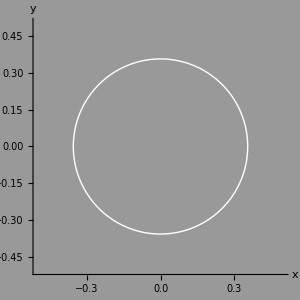
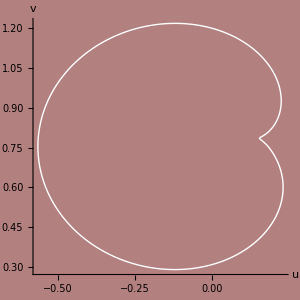
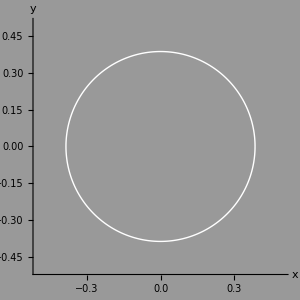
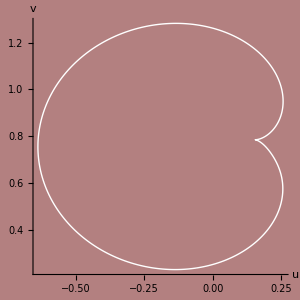
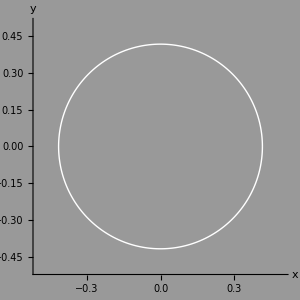
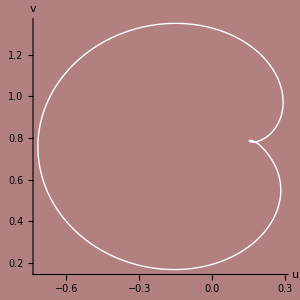
{{0.355595,-Graphics-,-Graphics-},{0.385595,-Graphics-,-Graphics-},{0.415595,-Graphics-,-Graphics-}}

```mathematica
Table[lists=Table[{r Cos[ang],r Sin[ang]},{r,{x}}];
pts=Transpose[#]&/@lists;
n=.5;
;
Flatten[{x,makeImage2[pts,expr,n]}],{x,Range[radius-.03,radius+.03,.03]}]
```